```mathematica
Clear["Global`*"]
```

```mathematica
(*Set Parameters*)
```

```mathematica
e = 4.8032047*10^-10*cm^(3/2)*g^(1/2)/s;
c = 2.9979246 * 10^10*cm/s;
kB = 1.380649 * 10^(-16)* g*cm^2/(k*s^2);
m = 9.1094*10^(-28)*g;
nv =  1* (cm^-3);
Bv = 30 *cm^(-1/2)*g^(1/2)/s;
thetab = 60*(Pi/180);
thetae = 10;
γ = thetae;
G = 6.6743*10^-8*cm^3/(g*s^2)
blkmass = 1.989*10^ 42*g;
```

```mathematica
(*Create functions*)
```

```mathematica
νB=e*Bv/(2*Pi*m*c);
νc = 3/2*νB*Sin[thetab]*γ^2;
Ii[x_]=2.5651(1+1.92x^(-1/3)+0.9977x^(-2/3))*Exp[-1.8899x^(1/3)];
j[ν_]=nv*e^2*ν / (2*Sqrt[3]*c*thetae^2)*Ii[(ν/νc)];
jx[x_]=nv*e^2*(x*νc) / (2*Sqrt[3]*c*thetae^2)*Ii[x];
brightTemp[ν_] =c^2 /(2*ν^2*kB)(10*G*blkmass / (c^2)*j[ν]);
```

```mathematica
(*Test functions*)
νB;
νc;
N[j[230*10^9*(1/s)]];
N[jx[1]];
Ii[10];
brightTemp[2.3*10^11(1/s)];
```

```mathematica
(*Plot functions*)
```

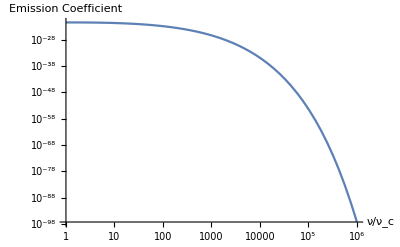

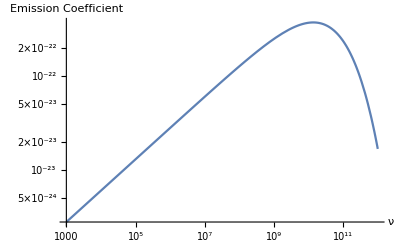

-Graphics-

```mathematica
LogLogPlot[jx[x] /.{g->1, cm->1, s->1}, {x, 1,10^6}, AxesLabel->{"ν/ν_c","Emission Coefficient"}]
LogLogPlot[j[x] /.{g->1, cm->1, s->1}, {x, 10^3,10^12}, AxesLabel->{"ν","Emission Coefficient"}]
Plot[brightTemp[ν]/.{k->1,g->1, cm->1, s->1}, {ν,1, 18}, AxesLabel->{"ν","Brightness Temperature"}]
```